```mathematica
MinVotedValues[primes_, count_] := Module[{ current,  maxdist, distanceTable, pos, fileName,  result,f },
result=Range[count];
pos=1;
current=0;
Monitor[
While[pos<= count,
result[[pos]]= current;
distanceTable = ParallelTable[Distance[current, p], {p, primes}];
pos++;
maxdist = Min[distanceTable];
If[maxdist==0,
current +=1;
,
current += maxdist;
];
];
, N[IntegerPart [pos/count * 10000]/100]
];
Return[result]
]
```

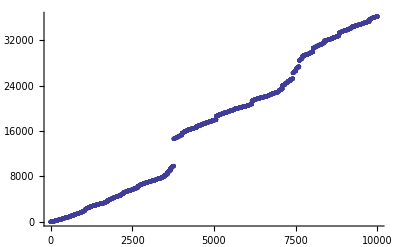

```mathematica
ListPlot[MinVotedValues[{3,5,7,11},10000]]
```

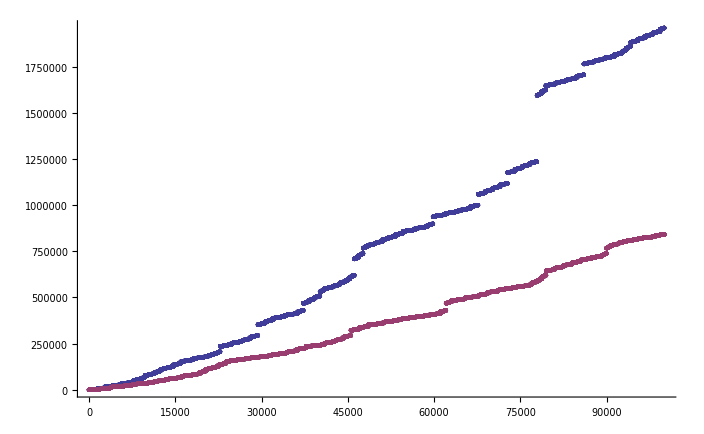

```mathematica
With[
{range=100000},
ListPlot[{
MinVotedValues[{3,5,7},range],
MinVotedValues[{3,5,7,11},range]
}]
]
```

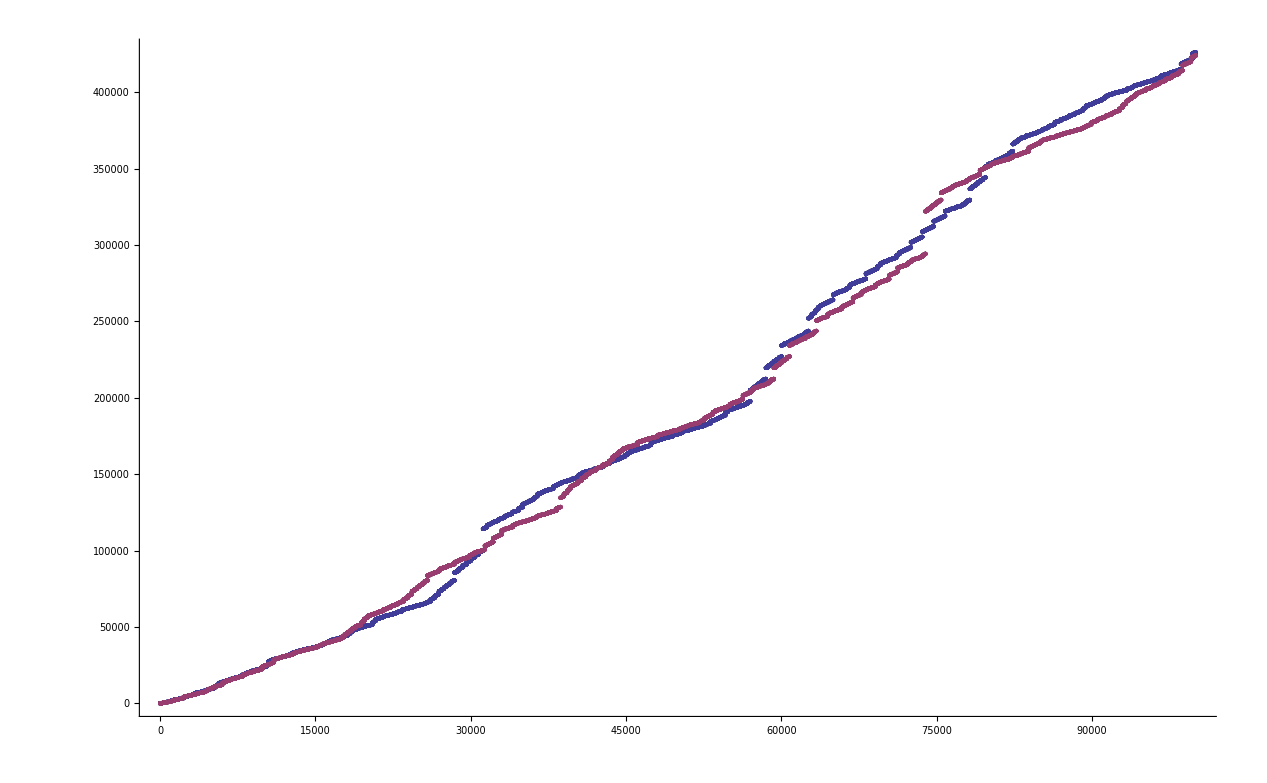

```mathematica
With[
{range=100000},
ListPlot[{
MinVotedValues[{7,11,13,19},range],
MinVotedValues[{7,11,13,17},range]
}]
]
```